```mathematica
f[t_]:=Piecewise[{{E^(-t+2π I t),t>=0&&t<=8},{0,t<0&&t>8}}]
```

```mathematica
h={ComplexExpand[Re[f[t]]],ComplexExpand[Im[f[t]]]}
g={ComplexExpand[Re[InverseFourierTransform[f[t],t,ω]]],ComplexExpand[Im[InverseFourierTransform[f[t],t,ω]]]}
```

{Re[Piecewise[{{ⅇ^(-t+2 ⅈ π t), t≥0&&t≤8}, {0, True}}]],Im[Piecewise[{{ⅇ^(-t+2 ⅈ π t), t≥0&&t≤8}, {0, True}}]]}

{1/(√(2 π) (1+(2 π-ω)^2))-Cos[8 ω]/(ⅇ^8 √(2 π) (1+(2 π-ω)^2))-(√(2 π) Sin[8 ω])/(ⅇ^8 (1+(2 π-ω)^2))+(ω Sin[8 ω])/(ⅇ^8 √(2 π) (1+(2 π-ω)^2)),(√(2 π))/(1+(2 π-ω)^2)-ω/(√(2 π) (1+(2 π-ω)^2))-(√(2 π) Cos[8 ω])/(ⅇ^8 (1+(2 π-ω)^2))+(ω Cos[8 ω])/(ⅇ^8 √(2 π) (1+(2 π-ω)^2))+Sin[8 ω]/(ⅇ^8 √(2 π) (1+(2 π-ω)^2))}

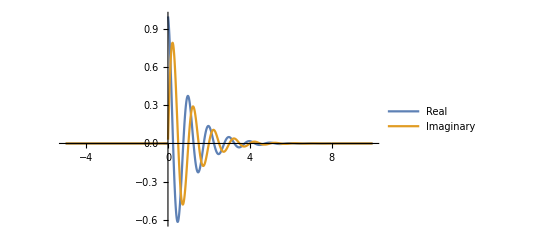

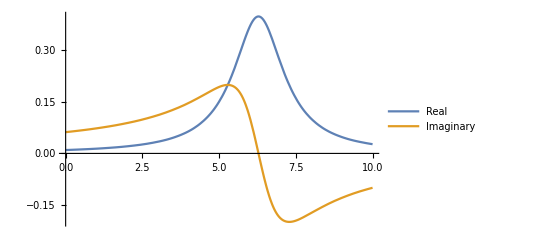

```mathematica
Plot[h,{t,-5,10},PlotRange->All,PlotLegends->{"Real","Imaginary"}]
Plot[g,{ω,0,10},PlotRange->All,PlotLegends->{"Real","Imaginary"}]
```